```mathematica
rateV3[mass_,δ_, mediator_]:=Module[{mx=mass,delta=δ, mV=mediator},
(*******************)
(* Free Parameters *)
(*******************)
Z=54; (* Atomic Number (Xenon) *)
A=131.904144; (* Atomic Mass (Xenon) *)
a=132;
mN=A 0.93149432; (* Nuclear Mass [GeV] (Xenon) *)


(********************)
(* Fixed Parameters *)
(********************)
mn=0.939;(* Neutron Mass [GeV] *)
rhox=0.3; (* Gev/cm^3 *)
nx[mx_]:=rhox/mx; (* cm^-3 *)
muN[mx_]:=(mx mN)/(mx+mN);(* GeV *)
mun[mx_]:=(mx mn)/(mx+mn);(* GeV *)
Nt=1/mN;(* GeV^-1 *)
alpha=1/137;
alphadark[mx_]:=3.7 10^-2(mx/(10^3(* GeV *)));


(*************************)
(* Velocity Distribution *)
(*************************)
light=2.99792458 10^5;(* km/s *)
v0=220(*km/s*); 
vE=232(*km/s*);
vesc=533(*km/s*); 
vmin[mx_,Er_,delta_]:=1/(√(2 Er mN))((Er mN)/muN[mx]+delta)light;  (* km/s *) (* [delta]=[Er]=GeV *) 
norm=π^(3/2)v0^3(Erf[vesc/v0] -(2 vesc)/(π^(1/2)v0)ⅇ^(-vesc^2/v0^2));  (* (km/s)^3 *)
VelDist[v_,θ_]:=(ⅇ^(-(v^2+vE^2+2 v vE θ)/v0^2))/norm;   (* (km/s)^-3 *)


(****************************)
(* Scattering Cross Section *)
(****************************)
q[Er_]:=√(2 Er  mN);(* GeV *) (* [Er]=GeV *)
b=√(mn^-1 10^3(45 a^(-1/2)-25 a^(-2/3))^-1); (* GeV^-1 *)
u[Er_]:=q[Er]^2 b^2/2; 
c1=-132.841;
c2=38.4859;
c3=-4.08455;
c4=0.153298;
c5=-0.0013897;
F[Er_]:=√(ⅇ^(-u[Er])/a^2(a+c1 u[Er]+c2 u[Er]^2+c3 u[Er]^3+c4 u[Er]^4+c5 u[Er]^5)^2); 
scat[mx_,v_,Er_]:=mN/(2(v/light)^2)(16 π Z^2)/((5.06 10^13)^2  (mV^2-delta^2+2mN Er)^2)F[Er]^2;      (* 1/ϵ^2 dσ/dEr GeV^-1 cm^2 *) 


(*******************)
(* Scattering Rate *)
(*******************) 
If[mV==10 10^-3,
If[mx<44,
Er0=Solve[vmin[mx,Er,delta]==vesc+vE,Er][[1]]; 
Er1=Solve[vmin[mx,Er,delta]==vesc+vE,Er][[2]]; 
func[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}]; 
rateEnergy7[Er_]= 2π nx[mx] Nt(10^5)Integrate[v^3 func[v]scat[mx,v,Er],{v,vmin[mx,Er,delta],vesc+vE}]; (* s^-1 GeV^-2 *)
Return[NIntegrate[rateEnergy7[Er],{Er,Er/.Er0 ,Er/.Er1}]](* s^-1 GeV^-1 *)
];
If[mx≥ 44,
Er0=Solve[vmin[mx,Er,delta]==vesc+vE,Er][[1]]; 
func[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}]; 
rateEnergy7[Er_]= 2π nx[mx] Nt(10^5)Integrate[v^3 func[v]scat[mx,v,Er],{v,vmin[mx,Er,delta],vesc+vE}];(* s^-1 GeV^-2 *)
Return[NIntegrate[rateEnergy7[Er],{Er,Er/.Er0 ,40.9 10^-6}]](* s^-1 GeV^-1 *)
];
];
If[mV==10,
If[mx≤24,
Er0=Solve[vmin[mx,Er,delta]==vesc+vE,Er][[2]];
func[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}]; 
rateEnergy7[Er_]= 2π nx[mx] Nt(10^5)Integrate[v^3 func[v]scat[mx,v,Er],{v,vmin[mx,Er,delta],vesc+vE}];(* s^-1 GeV^-2 *)
Return[NIntegrate[rateEnergy7[Er],{Er,4.9  10^-6,Er/.Er0}]](* s^-1 GeV^-1 *)
];
If[24<mx<31,
func[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}]; 
rateEnergy7[Er_]= 2π nx[mx] Nt(10^5)Integrate[v^3 func[v]scat[mx,v,Er],{v,vmin[mx,Er,delta],vesc+vE}];(* s^-1 GeV^-2 *)
Return[NIntegrate[rateEnergy7[Er],{Er,4.9  10^-6,40.9 10^-6}]](* s^-1 GeV^-1 *)
];
If[mx≥ 31,
func1[v_]=Integrate[VelDist[v,θ],{θ,-1,1}];
func2[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}];
rateEnergy[Er_]=   2π nx[mx] Nt(10^5) (Integrate[v^3 scat[mx,v,Er]func1[v],{v,vmin[mx,Er,delta],vesc-vE}]+Integrate[v^3 scat[mx,v,Er]func2[v],{v,vesc-vE,vesc+vE}]);  (* s^-1 GeV^-2 *)
Return[NIntegrate[rateEnergy[Er],{Er,4.9 10^-6,40.9 10^-6}]](* s^-1 GeV^-1 *)
];
];
]
```

```mathematica
(*******************************)
(* Velocity Integral condition *)
(*******************************)
(* mx < 31  then vmin never < vesc-vE *)
(* mx <= 24 then vmin may be > vesc+vE *)
(* mx >= 31 then vmin never > vesc+vE but always < vesc-vE *)
par=10;
par2=10 10^-6;
Reduce[vmin[par,Er,par2]< vesc-vE&& 4.9 10^-6≤ Er≤ 40.9 10^-6,Er,Reals]
Reduce[vmin[par,Er,par2]> vesc+vE&& 4.9 10^-6≤ Er≤ 40.9 10^-6,Er,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

False

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

7.48283×10^-6<Er≤0.0000409

```mathematica
Solve[vmin[par,Er,par2]==vesc+vE,Er][[2]]
```

{Er→7.48283×10^-6}

```mathematica
(*********************)
(* Experimental Data *)
(*********************)
10^3;(* Kg / Tonne*)
1.79 10^-27(* Kg / GeV *);
24 60 60 ;(* s/day *)
const=2.8(* event *)/(1.3 278.8(* tonne - day *)10^3/(1.79 10^-27)(* GeV/tonne *)24 60 60 (* s/day *))(* s^-1 GeV^-1 *)
```

1.60052×10^-37

```mathematica
(************************)
(* delta = 100 10^-6 GeV *)
(*** mV = 10 10^-3 GeV ***)
(************************)
```

```mathematica
step=(Log10[10^5]-Log10[40.96])/300;
stepin= Table[10^x,{x,Log10[40.96],Log10[10^5],step}];
```

```mathematica
datalist=Table[{i,Sqrt[16 π^2 const/rateV3[i,100 10^-6,10 10^-3]]},{i,stepin}]; 
datafunc=Interpolation[datalist, InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
checkdata={{4.184 10^1,9.333 10^-1},
{4.428 10^1,4.343 10^-9},
{4.690 10^1,1.888 10^-9},
{5.163 10^1,9.204 10^-10},
{6.096 10^1,4.799 10^-10},
{7.292 10^1,3.209 10^-10},
{1.000 10^2,2.212 10^-10},
{1.453 10^2,1.798 10^-10},
{2.024 10^2,1.725 10^-10},
{3.065 10^2,1.836 10^-10},
{4.540 10^2,1.988 10^-10},
{6.604 10^2,2.259 10^-10},
{1.010 10^3,2.650 10^-10},
{1.695 10^3,3.335 10^-10},
{2.597 10^3,4.034 10^-10},
{3.605 10^3,4.738 10^-10},
{4.776 10^3,5.383 10^-10},
{8.492 10^3,7.175 10^-10},
{1.453 10^4,9.382 10^-10},
{2.303 10^4,1.181 10^-9},
{5.356 10^4,1.799 10^-9},
{8.168 10^4,2.221 10^-9}};
checkfunc=Interpolation[checkdata,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {40.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

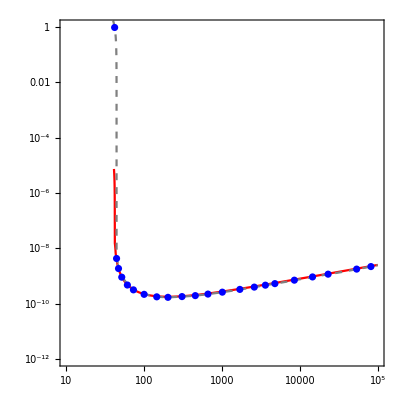

```mathematica
Show[LogLogPlot[datafunc[x],{x,41,10^5},PlotRange->{{10,10^5},{10^-12,10^0}},PlotStyle->Red],LogLogPlot[checkfunc[x],{x,40,46},PlotStyle->{Gray,Dashed}],LogLogPlot[checkfunc[x],{x,46,10^5},PlotStyle->{Gray,Dashed}],ListLogLogPlot[checkdata,PlotStyle->Blue],Frame-> True,AspectRatio->1]
```

```mathematica
(************************)
(** delta = 10 10^-6 GeV *)
(***** mV = 10 GeV ******)
(************************)
```

```mathematica
step2=(Log10[10^5]-Log10[8.151])/300;
stepin2= Table[10^x,{x,Log10[8.151],Log10[10^5],step2}];
```

```mathematica
datalist2=Table[{i,Sqrt[16 π^2 const/rateV3[i,10 10^-6,10 ]]},{i,stepin2}]; 
datafunc2=Interpolation[datalist2, InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
checkdata2={{8.151 10^0,8.319 10^-1},
{8.335 10^0,8.294 10^-3},
{8.661 10^0,2.551 10^-5},
{8.801 10^0,1.297 10^-5},
{9.145 10^0,6.748 10^-6},
{9.635 10^0,3.657 10^-6},
{1.066 10^1,1.658 10^-6},
{1.196 10^1,9.313 10^-7},
{1.412 10^1,5.131 10^-7},
{1.564 10^1,3.920 10^-7},
{2.166 10^1,2.245 10^-7},
{3.588 10^1,1.635 10^-7},
{6.841 10^1,1.682 10^-7},
{1.023 10^2,1.888 10^-7},
{2.001 10^2,2.471 10^-7},
{3.556 10^2,3.235 10^-7},
{6.199 10^2,4.234 10^-7},
{1.958 10^3,7.394 10^-7},
{3.756 10^3,1.025 10^-6},
{7.682 10^3,1.468 10^-6},
{1.348 10^4,1.946 10^-6},
{2.653 10^4,2.733 10^-6},
{5.495 10^4,3.939 10^-6}};
checkfunc2=Interpolation[checkdata2,InterpolationOrder->1]
```

InterpolatingFunction[…]

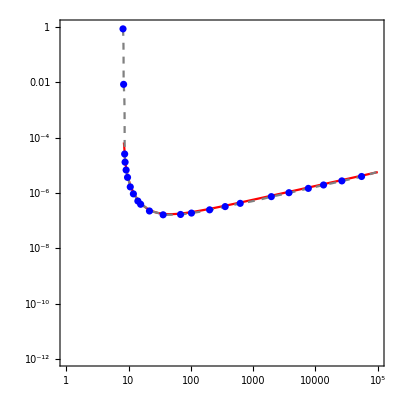

```mathematica
Show[LogLogPlot[datafunc2[x],{x,8.151,10^5},PlotRange->{{1,10^5},{10^-12,10^0}},PlotStyle->Red],LogLogPlot[checkfunc2[x],{x,8.151,10},PlotStyle->{Gray,Dashed}],LogLogPlot[checkfunc2[x],{x,10,10^5},PlotStyle->{Gray,Dashed}],ListLogLogPlot[checkdata2,PlotStyle->Blue],Frame-> True,AspectRatio->1]
```